```mathematica
DifusionV1[leftX_, rightX_, timeMax_, initialX_, leftCond_, rightCond_, stepX_, stepT_ ]:=Module[
{solution, tNum, xNum, xcurr,tcurr, x, time, hh},

xNum=Floor[(rightX-leftX)/stepX];
tNum =Floor[timeMax/stepT];

solution = Table[Table[0, {x,0,xNum}], {t, 0,tNum}];

hh =leftX;

For[i = 1 , i≤xNum+1, i++,
solution[[1, i]] = initialX[hh,0 ]//N;
hh= hh+stepX;
];

For[i=1, i≤tNum, i++,
solution[[i,1]] = leftCond;
solution[[i,xNum+1]] = rightCond;
];

tcurr=stepT;

For[time = 2, time≤tNum, time++,
xcurr = leftX + stepX;
For[x = 2, x≤xNum, x++,
solution[[time, x]] = (1-(2*stepT)/stepX^2)solution[[time-1, x]]+stepT/stepX^2(solution[[time-1, x-1]]+solution[[time-1,x+1]])//N;
xcurr = xcurr+stepX;
];
tcurr =tcurr+ stepT;
];

Return[solution];
]
```

```mathematica
initialX[x_,t_] := E^(-4π^2t)Sin[2π*x]//N;
res = DifusionV1[0,1, 0.1,initialX, 0,0, 0.01, 3*10^-5];
```

```mathematica
Animate[ListLinePlot[res[[i]], PlotRange->{-1,1}],{i,1,3334,1}, AnimationRunning->False ]
```

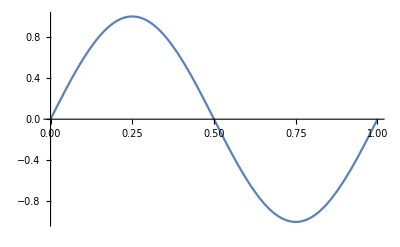

```mathematica
Plot[initialX[x,0], {x,0,1}]
```